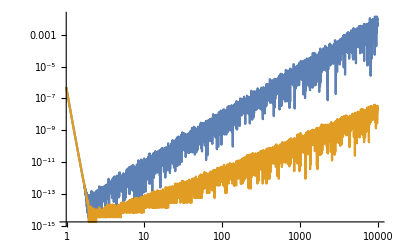

```mathematica
f[b_,r_]:=Module[{x,k2,Ek2, Kk2, ck, ce},
x=r/b;
k2=((1-(b-r))(1+(b-r)))/(4b r);
ce=2+14 x^2;
ck=-(1+5x+7 x^2+3 x^3);
Ek2=EllipticE[k2];
Kk2=EllipticK[k2];

2 b^3 √x(ce Ek2+ck Kk2) ];

g[b_,r_]:=Module[ {x,k2,Kk2,eps,del,EminusK},
x=r/b;
eps=x-1;
del=r-b;
k2=((1-(b-r))(1+(b-r)))/(4b r);
Kk2=EllipticK[k2];
EminusK=-π(0.25 k2+0.09375 k2^2+0.05859375 k2^3+0.042724609375 k2^4+0.0336456298828125 k2^5+0.027757644653320312 k2^6+0.023627042770385742 k2^7+0.020568184554576874 k2^8+0.018211413407698274 k2^9+0.016339684807462618 k2^10+0.01481712326858542 k2^11+0.013554300262740071 k2^12);

2 b^3 √x(EminusK(16+28eps+14 eps^2)-eps^2(2+3eps)Kk2) ];
LogLogPlot[{
Abs[f[r-0.25,r]-g[r-0.25,r]],
Abs[f[SetAccuracy[r-0.25,50],SetAccuracy[r,50]]-g[r-0.25,r]]
},{r,0.99,10000}]
```

```mathematica
s2[b_,r_,stable_]:= Module[{k2,ξ,EK,EE,EP,CoeffK,CoeffE,BadTerm,GoodTerm,Λ,taylor,x,eps,del,EminusK},
k2=((1-(b-r))(1+(b-r)))/(4 b r);
ξ=2b r(4-7 r^2-b^2);

EK=EllipticK[k2];
EE=EllipticE[k2];
EP=EllipticPi[1-1/(b-r)^2,k2];
CoeffK=8 -2 b^2 -3/(b r)+(12 r)/b-10 b r -14 r^2 -(6 r^3)/b;
CoeffE=-16 +4 b^2 +28 r^2 ;
x=r/b;
eps=x-1;
del=r-b;
EminusK=-π(0.25 k2+0.09375 k2^2+0.05859375 k2^3+0.042724609375 k2^4+0.0336456298828125 k2^5+0.027757644653320312 k2^6+0.023627042770385742 k2^7+0.020568184554576874 k2^8+0.018211413407698274 k2^9+0.016339684807462618 k2^10+0.01481712326858542 k2^11+0.013554300262740071 k2^12);

taylor=2 b^3 √x(EminusK(16+28eps+14 eps^2)-eps^2(2+3eps)EK);
If[stable,
BadTerm=taylor+ √(b r)( 8EK-16EE-3/(b r)EK+12(r/b)EK),
BadTerm=√(b r)(CoeffK *EK+CoeffE* EE)
];
GoodTerm=(3((b+r)/(b-r))EP)/(√(b r));
Λ=(BadTerm+GoodTerm)/(9π);
(2π)/3(1-3/2 Λ-HeavisideTheta[r-b])];
```

Power::infy: Infinite expression 1/0.^2 encountered.

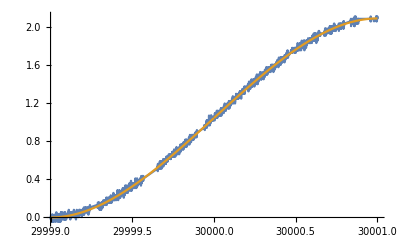

```mathematica
With[{r=3 10^4},Plot[
{s2[b,r,False],s2[b,r,True]}
,{b,r-1,r+1}]]
```

```mathematica
With[{r=3 10^4},Plot[
{s2[b,r,False]-s2[b,r,True]}
,{b,r-1,r+1}]]
```

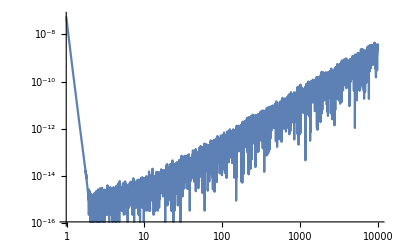

```mathematica
LogLogPlot[{
Abs[s2[SetAccuracy[r-0.25,30],SetAccuracy[r,30],False]-s2[r-0.25,r,True]]
},{r,0.99,10000}]
```